1.naloga
Obravnavaj met žogice iz višine H v smeri vektorja v0 = {v0x, v0y}. Upoštevaj gravitacijski pospešek g = 9.81 m/s 2. Pomagaj si z naslednjimi koraki:  

• Obravnavaj problem v ravnini, kjer je os x smer meta, os y pa predstavlja višino. Sestavi vektorsko (2D) funkcijo v[t_], ki za dan čas t izračuna vektor hitrosti pri metu. Izberi naslednje parametre:
v0 = {10, 3}
GG = 9.81
H = 10

```mathematica
v0={10,3};
GG=9.81;
H=10;
a = {0, -GG};
x0 ={0, H};
```

formule iz fizike:
v(t) = v_o + a t
x(t) = x_o + v_ot + at^2/2

```mathematica
v[t_] :={v0[[1]], v0[[2]] - GG*t}
{v0[[1]], v0[[2]] - GG*t}
v0 + a*t
```

{10,3-9.81 t}

{10,3-9.81 t}

• Vemo, da velja x(t) = x(0) +∫_0^t v(t)ⅆt. Če veš, da je x0 = {0, H}, sestavi še vektorsko funkcijo X[t_], ki vrne položaj žogice ob času t

Zapišimo sedaj obe funkciji kar preko vektorske oblike. Pozor: namesto simbola “mali x” smo uporabili simbol “veliki X”. To pa zato, ker si ponavadi simbolov x, y, ... ne želimo “zasesti”, saj imamo potem tipično težave pri reševanju enačb.

```mathematica
v[t_] := v0 + a*t
X[t_] := x0 + v0*t + a*t^2/2
```

```mathematica
v[1]
```

{10,-6.81}

• Sestavi funkcijo SlikaTocke[t_], ki nariše žogo kot točko. Velikost točke naj bo 3% slike.

Točko določa funkcija X[t]. S pomočjo te sestavimo ustrezen grafični objekt.

```mathematica
SlikaTocke[t_] := {PointSize[0.03],Point[X[t]]};
```

Oglejmo si rezultat. Pri vrednosti t = 1

```mathematica
Graphics[SlikaTocke[1]]
```

-Graphics-

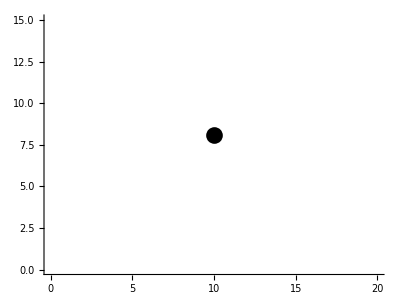

```mathematica
Graphics[SlikaTocke[1], Axes->True, PlotRange-> {{0,20}, {0, 15}}]
```

• Sestavi funkcijo SlikaVektorja[t_], ki nariše vektor hitrosti iz točke. Uporabi grafični objekt Arrow. Debelina črte naj bo 0,5% velikosti slike.

```mathematica
v[1]
v[2]
```

{10,-6.81}

{10,-16.62}

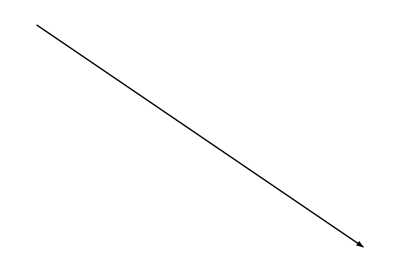

```mathematica
Graphics[Arrow[{{0,0}, v[1]}]]
```

Velikost puščice nastavimo z Arrowheads. S čim se nastavi debelina puščice?

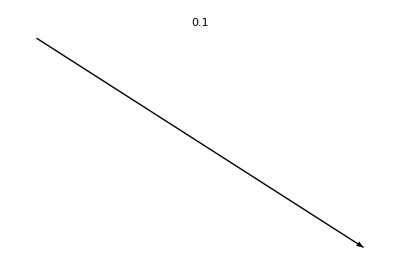
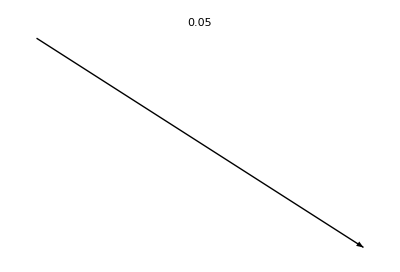
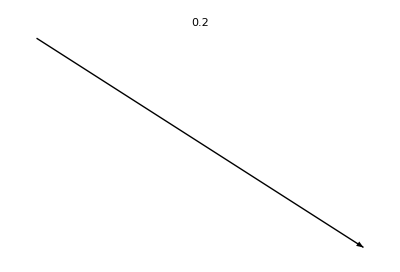

```mathematica
Table[Graphics[{Arrowheads[i],Arrow[{{0,0}, v[1]}]}, PlotLabel -> i], {i, {.1, .05, .2}}]
```

```mathematica
SlikaVektorja[t_] := {Arrow[{{0,0}, v[t]}]}
SlikaVektorja2[t_] := {Arrowheads[i], Arrow[{{0,0}, v[t]}]}
Table[Graphics[SlikaVektorja2[1]], {i, {.05}}]
```

{-Graphics-}

```mathematica
Graphics[SlikaVektorja[1]]
```

-Graphics-

• Nariši sliko žoge in vektorja po eni sekundi. Na sliki naj se nariše koordinatni sistem, os x nastavi na interval [−1, 25], os y pa na interval [−5, 15]. Velikosti enot na obeh oseh naj bosta enaki (Namig: preveri delovanje naslednjih opcij v objektu Graphics: Axes, PlotRange in AspectRatio).

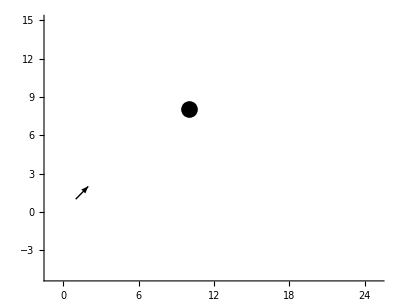

```mathematica
Graphics[{SlikaTocke[1], Arrow[{{1,1}, {2,2}}]}, Axes->True, PlotRange-> {{-1,25}, {-5, 15}}]
```

• S pomočjo funkcije Manipulate naredi animacijo leta žoge. Čas t premikaj o 0 do 5s.

```mathematica
Manipulate[Graphics[SlikaTocke[t], Axes->True, PlotRange-> {{-1,25}, {-5, 15}}], {t, 0, 5}]
```

• Izračunaj čas padca žoge. Izračunaj še vrednost v smeri x, kjer žoga pade.

To sem vse rešila prejšnji teden na vajah, a sem pozabila naložiti na git oz. poslati na mail. Prepišem ko pridem do šolskega kompa.

```mathematica
X[t][[2]] == 0
```

10+3 t-4.905 t^2==0

```mathematica
dolzinaHitrosti = (v0[[1]]^2+v0[[2]]^2)^(1/2)
sinkot =v0[[2]]/ dolzinaHitrosti //N
NajvišjeTočka = dolzinaHitrosti^2* sinkot^2 / (2*GG)+ H
```

√109

0.287348

10.4587

• Izračunaj čas doseganja največje višine leta ter maksimalno višino.

```mathematica
časLetaDonajvišjeTočke = 2*dolzinaHitrosti*sinkot/(GG *2)
domet  =dolzinaHitrosti^2 *Sin[2*ArcSin[sinkot]]/GG + H
```

0.30581

16.1162

```mathematica
časLeta= časLetaDonajvišjeTočke + (2*NajvišjeTočka/GG) ^(1/2)
```

1.76604

• Uporabi izračuna iz zgornjih dveh točk tako, da bo območje izrisa čimbolj primerno (na osi x od -1 do malce več kot lokacija padca; na osi y pa naj bo od nekaj pod ničlo do malce več kot maksimalna višina leta; čas animacije naj bo od 0 do trenutka padca.

```mathematica
Manipulate[Graphics[SlikaTocke[t], Axes->True, PlotRange-> {{-1,18}, {-1, 11}}], {t, 0, 1.76604}]
```

• Kakšna je absolutna vrednost hitrosti v trenutku, ko žogica zadene tla?

```mathematica
cas = v[časLeta]
```

{10.,-14.3248}

```mathematica
absHitrosti=((cas[[1]]) ^2 +  (cas[[1]]) ^2)^(1/2)
```

14.1421

2.naloga 
Ravnino podamo v obliki Ravnina[n_, v_], kjer je n normala na ravnino in je v točka na ravnini. Npr. ravnina, ki gre skozi točko (1, 1, 1) in je pravokotna na glavno diagonalo je r111 = Ravnina[{-1,-1,-1}, {1,1,1}].

• Sestavi funkcijo Slika[Ravnina[n_, v_]], ki pripravi 3D grafični objekt. Oglej si grafični objekt Hyperplane.

```mathematica
r111 = Ravnina[{-1,-1,-1},{1,1,1}]
Slika[Ravnina[n_, v_]] :=Hyperplane[n, v]
Slika[r111]
```

Ravnina[{-1,-1,-1},{1,1,1}]

Hyperplane[{-1,-1,-1},{1,1,1}]

• Sestavi funkcijo Format[r_Ravnina], ki nariše ravnino. Pozor: če definiramo funkcijo Format na objektih, se ti objekti “sami” izrišejo.

```mathematica
Format[r_Ravnina] := Graphics3D[Slika[r]]
r111
```

-Graphics3D-

• Sestavi še priročni funkciji Normala[Ravnina[n_, v_]] in Tocka[Ravnina[n_, v_]], ki vrneta točko in normalo ravnine.

```mathematica
Normala[Ravnina[n_,v_]]:=n
```

```mathematica
Tocka[Ravnina[n_,v_]]:=v
```

```mathematica
rx=Ravnina[{1, 0, 0}, {0, 0, 0}];
SlikaNormale[Ravnina[n_, v_]] :=Arrow[{v, v + n}]
```

```mathematica
Graphics3D[{Slika[r111],SlikaNormale[r111]}]
```

-Graphics3D-

```mathematica
ravnine = {r111, rx};
obeSliki[r_Ravnina] := {Slika[r],SlikaNormale[r]}
Graphics3D[Map[obeSliki, ravnine]]
```

-Graphics3D-

```mathematica
Graphics3D[Map[{Slika[#],SlikaNormale[#]}&, ravnine]]
```

-Graphics3D-

• Definiraj koordinatne ravnine rx, ry, rz, ki gredo skozi točko 0 in so njihove normale enotski vektorji koordinatnih osi.

```mathematica
rx:=Ravnina[{1,0,0},{0,0,0}]
ry:= Ravnina[{0,1,0},{0,0,0}]
rz:= Ravnina[{0,0,1},{0,0,0}]
```

• Sestavi funkcijo SlikaNormale[Ravnina[n_, v_]], ki vrne grafični objekt slike normale. Uporabi grafični objekt Arrow.

```mathematica
SlikaNormale[Ravnina[n_, v_]] :=Arrow[{v, v + n}]
```

```mathematica
Graphics3D[SlikaNormale[r111]]
```

-Graphics3D-

• Nariši vse štiri ravnine rx, ry, rz, r111 na isti sliki skupaj z normalami.

```mathematica
Graphics3D[{Slika[rx],Slika[ry],Slika[rz],Slika[r111]}]
```

-Graphics3D-

```mathematica
ravnine //
Map[obeSliki, #]& //
   Graphics3D[#]&
```

-Graphics3D-

• Sestavi funkcijo Enacba[Ravnina[n_, v_]], ki vrne enačbo ravnine.

```mathematica
Enacba[Ravnina[n_, v_]] := Module[{a, b, c, d},
	a = n[[1]];
	b = n[[2]];
	c = n[[3]]; 
	d = a*v[[1]] + b*v[[2]] + c*v[[3]];
	a*x + b*y + c*z == d]
obeSliki[r_Ravnina]:={Slika[r],SlikaNormale[r]}
Graphics3D[Map[obeSliki,ravnine]]
Enacba[r111]
```

-Graphics3D-

-x-y-z==-3

• Sestavi funkcijo ResiSistem[sistem_List], ki za dan sistem treh enačb v spremenljivkah x, y in z vrne točko rešitve. Predpostavi, da je sistem takšen, da vrne samo eno rešitev.

```mathematica
SezEnacb = List[Enacba[rx], Enacba[ry], Enacba[r111]];
ResiSistem[sistem_List] := Solve[{sistem[[1]], sistem[[2]], sistem[[3]]}, 
	{x, y, z}]
ResiSistem[SezEnacb]
```

{{x→0,y→0,z→3}}

• Sestavi funkcijo Presecisca[ravnine_List], ki za dan seznam ravnin poišče vse podmnožice velikosti 3 in potem poišče vse preseke treh ravnin iz teh podmnožic. Uporabi funkcijo Subset ter funkciji iz prejšnjih dveh nalog.

```mathematica
Presecisca[ravnine_List] :=ResiSistem[Map[Subset[Map[Enacba, ravnine], {n}], Enacba]]
```

• Sestavi funkcijo Vsebuje[Ravnina[n_, v_], x_, y_, z_, eps_:0.000001] , ki s toleranco 10^-6 natančno ugotovi, ali je točka v ravnini.  Uporabi definicijo ravnine n⃗·(OverVector[r_0]  −r⃗) = 0, kjer za vrednost na levi strani namesto enačenja z nič dopuščaš odmik za ϵ.

```mathematica
Vsebuje[Ravnina[n_,v_],x_,y_,z_,eps_:0.000001]:=Module[{tocka},
tocka = {x,y,z};
If[Dot[n, tocka]<eps, True];
If[Dot[n, tocka]>=eps, False]]
```

• Sestavi funkcijo Trikotnik[r_Ravnina, tocke_List], ki za dano ravnino in seznam točk nariše trikotnik na točkah, ki so vsebovane v ravnini. Predpostavimo, da bodo izmed točk podanih v seznamu točke, vedno natanko tri na ravnini - katere tri pa moramo izračunati. Izračunaj še vsa presečišča štirih ravnin (uporabi zgornjo funkcijo) ter trikotnik za ravnino rx.

```mathematica
Trikotnik[r_Ravnina,tocke_List]:= Graphics3D[Map[Line, Subsets[Vsebuje[r, tocke], 2]]]
```

• Sestavi funkcijo SlikaTrikotnikov[r1_, r2_, r3_, r4_], ki sestavi sliko vseh štirih trikotnikov, ki so definirani s preseki ravnin.

```mathematica
SlikaTrikotnikov[r1_,r2_,r3_,r4_] := Graphics3D[Map[Polygon, Subsets[{r1, r2, r3, r4}], {3}]]
```

3.naloga
Izberi si neko 3D telo in ga nariši s pomočjo točk in poligonov. Enostavni primeri so kocke,
kvadri. Bolj napredni so piramide, prizme, prerezane piramide. . . Bodite izvirni in narišite nekaj lepega.
Narišite tudi normalo nad eno ploskvijo, ki gleda ven iz telesa iz težišča ploskve.

```mathematica
v={{-1, -1, 0}, {-1, 1, 0}, {0, 0, -(1/Sqrt[2])}, 
  {0, 0, 1/Sqrt[2]}, {1, -1, 0}, {1, 1, 0}};
```

```mathematica
Graphics3D[GraphicsComplex[v,
 Polygon[{{4, 5, 6}, {4,6, 2}, {4, 2, 1}, {4, 1, 5}, {5, 1, 3}, {5, 3, 6}, 
   {3, 1, 2}, {6, 3, 2}}]]]
SlikaNormale[Ravnina[n_, v_]] :=Arrow[{v, v + n}]
```

-Graphics3D-

```mathematica
r = GraphicsComplex[v,
 Polygon[{{4, 5, 6}, {4,6, 2}, {4, 2, 1}, {4, 1, 5}, {5, 1, 3}, {5, 3, 6}, 
   {3, 1, 2}, {6, 3, 2}}]];
```

```mathematica
Graphics3D[ {r, SlikaNormale[Ravnina[{-1, -1, 0}, {-1, 1, 0}]]}]
```

-Graphics3D-